Numerical Solver of 1D Infinite Well
This script is a numerical Solver for the 1D infinite well scenario utilising finite differences of the second order derivative.

## Preparing Values

m is mass, where here it is set to that of the electron rest mass in eV·s^2·m^-2.
A is the width of the infinite well in m^2.
a is the width of the segments of the infinite well for the finite differences approximation, in the same units.

```mathematica
m = 0.511*10^6/(9*10^16);
A = 0.53*10^-10;
a = A/101;
```

n is the number of steps segmenting the domain of the infinite well.

```mathematica
n = 100;
```

## Preparing Eigensystem

```mathematica
getMatrixElement[x_,y_] := 
If [x==y, 2,
If[x==y-1, -1,
If[x==y+1,-1, 0]]];
```

Here we construct the matrix resulting from applying the finite differences approximation to the TISE.

```mathematica
finiteDifferencesMatrix = Table[
Table [
getMatrixElement[j,i]
,{j, 1, n}]
,{i, 1, n}];
```

## Solving Eigenproblem and Plotting Results

Solve the eigenproblem and obtain the resulting eigensystem.

```mathematica
eigensystem = Eigensystem[finiteDifferencesMatrix];
```

This shows the first harmonic of the wave function for a particle in the constructed infinite well, and its respective energy.

```mathematica
((N[eigensystem[[1,-1]]] * ((6.582*10^-16)^2)) / (2 * m * (a^2)))
```

134.036

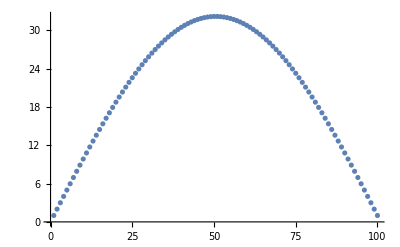

```mathematica
ListPlot[eigensystem[[2,-1]]]
```

This shows the second harmonic of the wave function for a particle in the constructed infinite well, and its respective energy.

```mathematica
((N[eigensystem[[1,-2]]] * ((6.582*10^-16)^2)) / (2 * m * (a^2)))
```

536.013

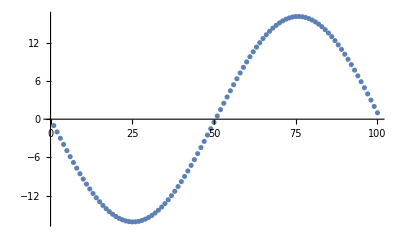

```mathematica
ListPlot[eigensystem[[2,-2]]]
```

This shows the third harmonic of the wave function for a particle in the constructed infinite well, and its respective energy.

```mathematica
((N[eigensystem[[1,-3]]] * ((6.582*10^-16)^2)) / (2 * m * (a^2)))
```

1205.54

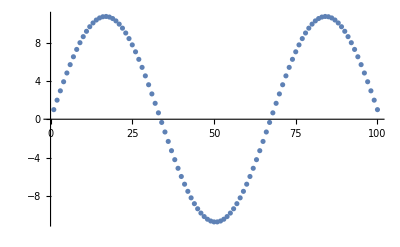

```mathematica
ListPlot[eigensystem[[2,-3]]]
```

This shows the fourth harmonic of the wave function for a particle in the constructed infinite well, and its respective energy.

```mathematica
((N[eigensystem[[1,-4]]] * ((6.582*10^-16)^2)) / (2 * m * (a^2)))
```

2141.98

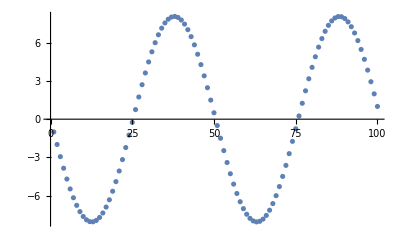

```mathematica
ListPlot[eigensystem[[2,-4]]]
```

## Exploring Progression of Error

Here we plot the actual eigenvalues (orange) against the eigenvalues obtained via the approximation (blue) to show how accuracy is lost towards the halfway-eigenvalue after which the approximation begins to deviate from the actual value rapidly, converging on

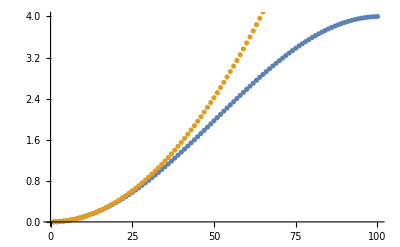

```mathematica
ListPlot[{Reverse[Eigenvalues[finiteDifferencesMatrix]],Flatten[Table[a^2*x^2*Pi^2/A^2,{x,100}]]}, PlotRange->{0,4}]
```